## Init

```mathematica
k4rob =Select[ , Last[#]>100&];
k4reg= Select[,Last[#]>100&];
```

```mathematica
psrob =
```

```mathematica
msrob = N[Mean/@ psrob];
```

```mathematica
psreg =
```

```mathematica
msreg = N[Mean/@ psreg];
```

```mathematica
sirob = SortBy[Range[Length[k4rob]], msrob[[#]]&];
```

```mathematica
sireg = SortBy[Range[Length[k4reg]], msreg[[#]]&];
```

```mathematica
ru = k4rob[[sirob[[15]],1]];
{n, k, r} = ru;
pat = getca[ru, 200];
ca = pat;
lt = TestCALifeTime[ca];
```

```mathematica
ClearAll@PerturbPopulation
```

```mathematica
getcancerperts[ru_, bitfunc_:("AddValue"->1)]:= Module[{ca =getca[ru], perts}, 
perts =getbodyrules[ca, bitfunc];
Select[perts, (TestCALifeTime[PerturbCA[{ca, ru}, #]] == -Infinity&)]]
```

```mathematica
gethealers[ru_, rowidx_->colspec_, healfunc_:(#!=-Infinity&),bitfunc_:("AddValue"->1)]:= 
Module[{ca = PerturbCA[{getca[ru],ru} , rowidx->colspec], rules}, 
rules = getbodyrules[ca, bitfunc];
Select[Select[rules, #[[1]]>rowidx&], healfunc[TestCALifeTime[PerturbCA[{ca, ru}, #]]]&]]
```

```mathematica
PerturbPopulation[{n_Integer, k_Integer, r_Integer}, sample_:10, pertspec_:("Random"->1)]:= Module[{rus =quickneutral[{n, k, r}], s},
 s = If[sample ===All, Length[rus], sample];
PerturbPopulation[RandomSample[quickneutral[{n, k, r}], UpTo[s]],  pertspec]]
```

```mathematica
PerturbPopulation[rus_, pertspec_:("Random"->1)]:= PerturbPopulation[getca/@ rus, rus, pertspec]
```

```mathematica
PerturbPopulation[cas_, rus_, pertspec_]:= 
With[{ps = If[pertspec[[1]] == "Random", RandomChoice[getbodyrules[cas[[1]], "AddValue"->1]], pertspec]},PerturbCA[{#1, #2}, ps]&@@@Transpose[{cas, rus}]]
```

```mathematica
ClearAll@TherapySensitivityPlot
```

```mathematica
TherapySensitivityPlot[ru_, rowidx_->colspec_]:= Module[{ca = getca[ru]},
pca = PerturbCA[{ca, ru}, rowidx->colspec];
idxs = getbodyidxs[pca];
idxfunc =  idxs[[rowidx+1;;]]&;
sensitivities = PerturbationSensitivities[{pca, ru}, (absdeltalt[ca, #2]&), ("AddValue"->1), "IndexFunction"->idxfunc];
pertreps = {rowidx, #}->Red&/@tofullform[expandrange[colspec, Length[idxs[[rowidx]]]]][[1]];
marked = ReplacePart[Join[idxs[[;;rowidx]]/. {_Integer, _Integer}->LightGray,sensitivities], pertreps];
PlotSensitivities[pca, marked]
]
```

### Getting fitness-neutral group

```mathematica
ng1 = NestGraph[exhaustiveneutral, {ru}, 3];
```

```mathematica
patients = VertexList[ng1];
```

```mathematica
patients  = quickneutral[ru];
```

## Population Responses

### To diseases

For big yellow, if one of them dies, they all pretty much get die

```mathematica
pcarus = {getca[#], #}&/@ patients;
```

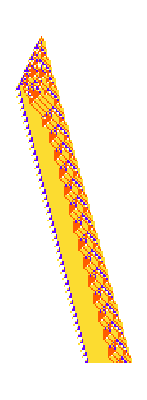

```mathematica
PlotCA[PerturbCA[{ca,patients[[1]]},2-> {{1},"Enumerate","AddValue"->1}]]
```

```mathematica
cancerperts = getcancerperts[patients[[1]]]
```

201

{2→{{1},Enumerate,AddValue→1},5→{{4},Enumerate,AddValue→1},6→{{4},Enumerate,AddValue→1},6→{{5},Enumerate,AddValue→1},7→{{2},Enumerate,AddValue→1},7→{{5},Enumerate,AddValue→1},7→{{6},Enumerate,AddValue→1},8→{{5},Enumerate,AddValue→1},8→{{7},Enumerate,AddValue→1},9→{{5},Enumerate,AddValue→1},10→{{10},Enumerate,AddValue→1},11→{{3},Enumerate,AddValue→1},11→{{5},Enumerate,AddValue→1},11→{{6},Enumerate,AddValue→1},11→{{8},Enumerate,AddValue→1},12→{{6},Enumerate,AddValue→1},12→{{10},Enumerate,AddValue→1},12→{{11},Enumerate,AddValue→1},13→{{7},Enumerate,AddValue→1},14→{{2},Enumerate,AddValue→1},15→{{2},Enumerate,AddValue→1},15→{{5},Enumerate,AddValue→1},15→{{10},Enumerate,AddValue→1},16→{{4},Enumerate,AddValue→1},16→{{7},Enumerate,AddValue→1},17→{{8},Enumerate,AddValue→1},17→{{12},Enumerate,AddValue→1},18→{{4},Enumerate,AddValue→1},18→{{6},Enumerate,AddValue→1},18→{{9},Enumerate,AddValue→1},18→{{10},Enumerate,AddValue→1},18→{{12},Enumerate,AddValue→1},19→{{9},Enumerate,AddValue→1},19→{{12},Enumerate,AddValue→1},20→{{2},Enumerate,AddValue→1},20→{{6},Enumerate,AddValue→1},20→{{9},Enumerate,AddValue→1},21→{{1},Enumerate,AddValue→1},21→{{6},Enumerate,AddValue→1},21→{{7},Enumerate,AddValue→1},21→{{8},Enumerate,AddValue→1},21→{{10},Enumerate,AddValue→1},22→{{1},Enumerate,AddValue→1},22→{{4},Enumerate,AddValue→1},22→{{7},Enumerate,AddValue→1},22→{{8},Enumerate,AddValue→1},22→{{11},Enumerate,AddValue→1},23→{{1},Enumerate,AddValue→1},23→{{4},Enumerate,AddValue→1},23→{{9},Enumerate,AddValue→1},24→{{5},Enumerate,AddValue→1},24→{{6},Enumerate,AddValue→1},24→{{7},Enumerate,AddValue→1},24→{{9},Enumerate,AddValue→1},24→{{11},Enumerate,AddValue→1},24→{{13},Enumerate,AddValue→1},25→{{2},Enumerate,AddValue→1},25→{{6},Enumerate,AddValue→1},25→{{7},Enumerate,AddValue→1},25→{{11},Enumerate,AddValue→1},26→{{1},Enumerate,AddValue→1},26→{{4},Enumerate,AddValue→1},26→{{5},Enumerate,AddValue→1},26→{{6},Enumerate,AddValue→1},26→{{7},Enumerate,AddValue→1},26→{{9},Enumerate,AddValue→1},26→{{13},Enumerate,AddValue→1},27→{{4},Enumerate,AddValue→1},27→{{5},Enumerate,AddValue→1},27→{{9},Enumerate,AddValue→1},28→{{1},Enumerate,AddValue→1},28→{{4},Enumerate,AddValue→1},28→{{5},Enumerate,AddValue→1},29→{{1},Enumerate,AddValue→1},29→{{4},Enumerate,AddValue→1},29→{{6},Enumerate,AddValue→1},29→{{7},Enumerate,AddValue→1},29→{{8},Enumerate,AddValue→1},29→{{9},Enumerate,AddValue→1},30→{{1},Enumerate,AddValue→1},30→{{3},Enumerate,AddValue→1},30→{{12},Enumerate,AddValue→1},31→{{2},Enumerate,AddValue→1},31→{{4},Enumerate,AddValue→1},31→{{6},Enumerate,AddValue→1},31→{{7},Enumerate,AddValue→1},31→{{8},Enumerate,AddValue→1},31→{{10},Enumerate,AddValue→1},31→{{19},Enumerate,AddValue→1},32→{{2},Enumerate,AddValue→1},32→{{3},Enumerate,AddValue→1},32→{{5},Enumerate,AddValue→1},32→{{8},Enumerate,AddValue→1},32→{{9},Enumerate,AddValue→1},33→{{2},Enumerate,AddValue→1},33→{{3},Enumerate,AddValue→1},33→{{4},Enumerate,AddValue→1},33→{{5},Enumerate,AddValue→1},33→{{6},Enumerate,AddValue→1},33→{{8},Enumerate,AddValue→1},33→{{9},Enumerate,AddValue→1},34→{{1},Enumerate,AddValue→1},34→{{2},Enumerate,AddValue→1},34→{{3},Enumerate,AddValue→1},34→{{6},Enumerate,AddValue→1},35→{{1},Enumerate,AddValue→1},35→{{2},Enumerate,AddValue→1},35→{{3},Enumerate,AddValue→1},35→{{4},Enumerate,AddValue→1},35→{{5},Enumerate,AddValue→1},35→{{6},Enumerate,AddValue→1},35→{{9},Enumerate,AddValue→1},35→{{17},Enumerate,AddValue→1},36→{{1},Enumerate,AddValue→1},36→{{2},Enumerate,AddValue→1},36→{{3},Enumerate,AddValue→1},36→{{4},Enumerate,AddValue→1},36→{{5},Enumerate,AddValue→1},36→{{8},Enumerate,AddValue→1},36→{{13},Enumerate,AddValue→1},36→{{14},Enumerate,AddValue→1},36→{{20},Enumerate,AddValue→1},37→{{2},Enumerate,AddValue→1},37→{{3},Enumerate,AddValue→1},37→{{4},Enumerate,AddValue→1},37→{{8},Enumerate,AddValue→1},38→{{1},Enumerate,AddValue→1},38→{{2},Enumerate,AddValue→1},38→{{3},Enumerate,AddValue→1},38→{{8},Enumerate,AddValue→1},38→{{10},Enumerate,AddValue→1},39→{{2},Enumerate,AddValue→1},39→{{3},Enumerate,AddValue→1},39→{{6},Enumerate,AddValue→1},39→{{7},Enumerate,AddValue→1},39→{{10},Enumerate,AddValue→1},39→{{16},Enumerate,AddValue→1},40→{{3},Enumerate,AddValue→1},40→{{4},Enumerate,AddValue→1},40→{{6},Enumerate,AddValue→1},40→{{8},Enumerate,AddValue→1},40→{{20},Enumerate,AddValue→1},40→{{22},Enumerate,AddValue→1},41→{{3},Enumerate,AddValue→1},41→{{4},Enumerate,AddValue→1},41→{{5},Enumerate,AddValue→1},41→{{6},Enumerate,AddValue→1},41→{{19},Enumerate,AddValue→1},42→{{2},Enumerate,AddValue→1},42→{{3},Enumerate,AddValue→1},42→{{4},Enumerate,AddValue→1},42→{{5},Enumerate,AddValue→1},42→{{6},Enumerate,AddValue→1},42→{{7},Enumerate,AddValue→1},42→{{8},Enumerate,AddValue→1},43→{{2},Enumerate,AddValue→1},43→{{3},Enumerate,AddValue→1},43→{{11},Enumerate,AddValue→1},43→{{14},Enumerate,AddValue→1},44→{{3},Enumerate,AddValue→1},44→{{4},Enumerate,AddValue→1},44→{{5},Enumerate,AddValue→1},44→{{24},Enumerate,AddValue→1},45→{{4},Enumerate,AddValue→1},45→{{5},Enumerate,AddValue→1},45→{{6},Enumerate,AddValue→1},45→{{7},Enumerate,AddValue→1},45→{{14},Enumerate,AddValue→1},46→{{2},Enumerate,AddValue→1},46→{{3},Enumerate,AddValue→1},46→{{5},Enumerate,AddValue→1},46→{{21},Enumerate,AddValue→1},47→{{2},Enumerate,AddValue→1},47→{{3},Enumerate,AddValue→1},47→{{13},Enumerate,AddValue→1},47→{{17},Enumerate,AddValue→1},48→{{3},Enumerate,AddValue→1},48→{{4},Enumerate,AddValue→1},48→{{5},Enumerate,AddValue→1},48→{{6},Enumerate,AddValue→1},48→{{8},Enumerate,AddValue→1},49→{{4},Enumerate,AddValue→1},49→{{5},Enumerate,AddValue→1},49→{{8},Enumerate,AddValue→1},49→{{11},Enumerate,AddValue→1},49→{{14},Enumerate,AddValue→1},49→{{15},Enumerate,AddValue→1},49→{{16},Enumerate,AddValue→1},50→{{2},Enumerate,AddValue→1},50→{{3},Enumerate,AddValue→1},50→{{5},Enumerate,AddValue→1},50→{{7},Enumerate,AddValue→1},50→{{17},Enumerate,AddValue→1},51→{{2},Enumerate,AddValue→1},51→{{3},Enumerate,AddValue→1},51→{{7},Enumerate,AddValue→1},51→{{13},Enumerate,AddValue→1},52→{{3},Enumerate,AddValue→1},52→{{4},Enumerate,AddValue→1},52→{{5},Enumerate,AddValue→1},52→{{16},Enumerate,AddValue→1},53→{{4},Enumerate,AddValue→1},53→{{5},Enumerate,AddValue→1},53→{{11},Enumerate,AddValue→1},54→{{2},Enumerate,AddValue→1},54→{{3},Enumerate,AddValue→1},54→{{5},Enumerate,AddValue→1},54→{{6},Enumerate,AddValue→1},54→{{7},Enumerate,AddValue→1},54→{{11},Enumerate,AddValue→1},55→{{2},Enumerate,AddValue→1},55→{{3},Enumerate,AddValue→1},55→{{4},Enumerate,AddValue→1},55→{{5},Enumerate,AddValue→1},56→{{3},Enumerate,AddValue→1},56→{{4},Enumerate,AddValue→1},56→{{5},Enumerate,AddValue→1},56→{{6},Enumerate,AddValue→1},56→{{7},Enumerate,AddValue→1},56→{{10},Enumerate,AddValue→1},57→{{4},Enumerate,AddValue→1},57→{{5},Enumerate,AddValue→1},57→{{7},Enumerate,AddValue→1},57→{{8},Enumerate,AddValue→1},57→{{9},Enumerate,AddValue→1},57→{{10},Enumerate,AddValue→1},58→{{2},Enumerate,AddValue→1},58→{{3},Enumerate,AddValue→1},58→{{5},Enumerate,AddValue→1},58→{{6},Enumerate,AddValue→1},58→{{7},Enumerate,AddValue→1},58→{{9},Enumerate,AddValue→1},58→{{10},Enumerate,AddValue→1},58→{{11},Enumerate,AddValue→1},59→{{2},Enumerate,AddValue→1},59→{{3},Enumerate,AddValue→1},59→{{4},Enumerate,AddValue→1},59→{{5},Enumerate,AddValue→1},59→{{7},Enumerate,AddValue→1},60→{{3},Enumerate,AddValue→1},60→{{4},Enumerate,AddValue→1},60→{{5},Enumerate,AddValue→1},60→{{6},Enumerate,AddValue→1},60→{{7},Enumerate,AddValue→1},60→{{9},Enumerate,AddValue→1},61→{{4},Enumerate,AddValue→1},61→{{5},Enumerate,AddValue→1},61→{{7},Enumerate,AddValue→1},61→{{8},Enumerate,AddValue→1},61→{{10},Enumerate,AddValue→1},61→{{16},Enumerate,AddValue→1},62→{{2},Enumerate,AddValue→1},62→{{3},Enumerate,AddValue→1},62→{{5},Enumerate,AddValue→1},62→{{6},Enumerate,AddValue→1},62→{{7},Enumerate,AddValue→1},62→{{9},Enumerate,AddValue→1},62→{{10},Enumerate,AddValue→1},62→{{12},Enumerate,AddValue→1},63→{{2},Enumerate,AddValue→1},63→{{3},Enumerate,AddValue→1},63→{{5},Enumerate,AddValue→1},63→{{7},Enumerate,AddValue→1},63→{{8},Enumerate,AddValue→1},63→{{10},Enumerate,AddValue→1},63→{{16},Enumerate,AddValue→1},64→{{3},Enumerate,AddValue→1},64→{{4},Enumerate,AddValue→1},64→{{5},Enumerate,AddValue→1},64→{{7},Enumerate,AddValue→1},64→{{9},Enumerate,AddValue→1},64→{{10},Enumerate,AddValue→1},64→{{12},Enumerate,AddValue→1},65→{{4},Enumerate,AddValue→1},65→{{5},Enumerate,AddValue→1},65→{{8},Enumerate,AddValue→1},65→{{10},Enumerate,AddValue→1},65→{{11},Enumerate,AddValue→1},65→{{13},Enumerate,AddValue→1},66→{{2},Enumerate,AddValue→1},66→{{3},Enumerate,AddValue→1},66→{{5},Enumerate,AddValue→1},66→{{6},Enumerate,AddValue→1},66→{{7},Enumerate,AddValue→1},66→{{10},Enumerate,AddValue→1},66→{{12},Enumerate,AddValue→1},66→{{13},Enumerate,AddValue→1},66→{{15},Enumerate,AddValue→1},67→{{2},Enumerate,AddValue→1},67→{{3},Enumerate,AddValue→1},67→{{5},Enumerate,AddValue→1},67→{{8},Enumerate,AddValue→1},67→{{10},Enumerate,AddValue→1},67→{{11},Enumerate,AddValue→1},67→{{23},Enumerate,AddValue→1},68→{{3},Enumerate,AddValue→1},68→{{4},Enumerate,AddValue→1},68→{{5},Enumerate,AddValue→1},68→{{7},Enumerate,AddValue→1},68→{{10},Enumerate,AddValue→1},68→{{12},Enumerate,AddValue→1},68→{{13},Enumerate,AddValue→1},69→{{4},Enumerate,AddValue→1},69→{{5},Enumerate,AddValue→1},69→{{8},Enumerate,AddValue→1},69→{{11},Enumerate,AddValue→1},69→{{13},Enumerate,AddValue→1},69→{{14},Enumerate,AddValue→1},69→{{17},Enumerate,AddValue→1},70→{{2},Enumerate,AddValue→1},70→{{3},Enumerate,AddValue→1},70→{{5},Enumerate,AddValue→1},70→{{6},Enumerate,AddValue→1},70→{{10},Enumerate,AddValue→1},70→{{13},Enumerate,AddValue→1},70→{{15},Enumerate,AddValue→1},70→{{16},Enumerate,AddValue→1},70→{{17},Enumerate,AddValue→1},70→{{18},Enumerate,AddValue→1},71→{{2},Enumerate,AddValue→1},71→{{3},Enumerate,AddValue→1},71→{{8},Enumerate,AddValue→1},71→{{11},Enumerate,AddValue→1},71→{{13},Enumerate,AddValue→1},71→{{14},Enumerate,AddValue→1},71→{{15},Enumerate,AddValue→1},72→{{3},Enumerate,AddValue→1},72→{{4},Enumerate,AddValue→1},72→{{5},Enumerate,AddValue→1},72→{{10},Enumerate,AddValue→1},72→{{13},Enumerate,AddValue→1},72→{{14},Enumerate,AddValue→1},72→{{15},Enumerate,AddValue→1},72→{{16},Enumerate,AddValue→1},73→{{4},Enumerate,AddValue→1},73→{{5},Enumerate,AddValue→1},73→{{11},Enumerate,AddValue→1},73→{{14},Enumerate,AddValue→1},73→{{15},Enumerate,AddValue→1},73→{{16},Enumerate,AddValue→1},73→{{17},Enumerate,AddValue→1},74→{{2},Enumerate,AddValue→1},74→{{3},Enumerate,AddValue→1},74→{{5},Enumerate,AddValue→1},74→{{6},Enumerate,AddValue→1},74→{{13},Enumerate,AddValue→1},74→{{16},Enumerate,AddValue→1},74→{{18},Enumerate,AddValue→1},74→{{19},Enumerate,AddValue→1},75→{{2},Enumerate,AddValue→1},75→{{3},Enumerate,AddValue→1},75→{{11},Enumerate,AddValue→1},75→{{14},Enumerate,AddValue→1},75→{{15},Enumerate,AddValue→1},75→{{16},Enumerate,AddValue→1},75→{{17},Enumerate,AddValue→1},76→{{3},Enumerate,AddValue→1},76→{{4},Enumerate,AddValue→1},76→{{5},Enumerate,AddValue→1},76→{{13},Enumerate,AddValue→1},76→{{16},Enumerate,AddValue→1},76→{{17},Enumerate,AddValue→1},77→{{4},Enumerate,AddValue→1},77→{{5},Enumerate,AddValue→1},77→{{14},Enumerate,AddValue→1},77→{{17},Enumerate,AddValue→1},77→{{18},Enumerate,AddValue→1},78→{{2},Enumerate,AddValue→1},78→{{3},Enumerate,AddValue→1},78→{{5},Enumerate,AddValue→1},78→{{6},Enumerate,AddValue→1},78→{{16},Enumerate,AddValue→1},78→{{18},Enumerate,AddValue→1},78→{{26},Enumerate,AddValue→1},79→{{2},Enumerate,AddValue→1},79→{{3},Enumerate,AddValue→1},79→{{14},Enumerate,AddValue→1},79→{{18},Enumerate,AddValue→1},80→{{3},Enumerate,AddValue→1},80→{{4},Enumerate,AddValue→1},80→{{5},Enumerate,AddValue→1},80→{{16},Enumerate,AddValue→1},80→{{18},Enumerate,AddValue→1},80→{{19},Enumerate,AddValue→1},81→{{4},Enumerate,AddValue→1},81→{{5},Enumerate,AddValue→1},81→{{17},Enumerate,AddValue→1},81→{{21},Enumerate,AddValue→1},82→{{2},Enumerate,AddValue→1},82→{{3},Enumerate,AddValue→1},82→{{5},Enumerate,AddValue→1},82→{{6},Enumerate,AddValue→1},82→{{19},Enumerate,AddValue→1},82→{{21},Enumerate,AddValue→1},82→{{22},Enumerate,AddValue→1},83→{{2},Enumerate,AddValue→1},83→{{3},Enumerate,AddValue→1},83→{{17},Enumerate,AddValue→1},83→{{21},Enumerate,AddValue→1},84→{{3},Enumerate,AddValue→1},84→{{4},Enumerate,AddValue→1},84→{{5},Enumerate,AddValue→1},84→{{19},Enumerate,AddValue→1},85→{{4},Enumerate,AddValue→1},85→{{5},Enumerate,AddValue→1},86→{{2},Enumerate,AddValue→1},86→{{3},Enumerate,AddValue→1},86→{{5},Enumerate,AddValue→1},86→{{6},Enumerate,AddValue→1},86→{{21},Enumerate,AddValue→1},87→{{2},Enumerate,AddValue→1},87→{{3},Enumerate,AddValue→1},88→{{3},Enumerate,AddValue→1},88→{{4},Enumerate,AddValue→1},88→{{5},Enumerate,AddValue→1},88→{{21},Enumerate,AddValue→1},88→{{22},Enumerate,AddValue→1},88→{{24},Enumerate,AddValue→1},89→{{4},Enumerate,AddValue→1},89→{{5},Enumerate,AddValue→1},90→{{2},Enumerate,AddValue→1},90→{{3},Enumerate,AddValue→1},90→{{5},Enumerate,AddValue→1},90→{{6},Enumerate,AddValue→1},90→{{24},Enumerate,AddValue→1},90→{{25},Enumerate,AddValue→1},91→{{2},Enumerate,AddValue→1},91→{{3},Enumerate,AddValue→1},92→{{3},Enumerate,AddValue→1},92→{{4},Enumerate,AddValue→1},92→{{5},Enumerate,AddValue→1},93→{{4},Enumerate,AddValue→1},93→{{5},Enumerate,AddValue→1},94→{{2},Enumerate,AddValue→1},94→{{3},Enumerate,AddValue→1},94→{{5},Enumerate,AddValue→1},94→{{6},Enumerate,AddValue→1},95→{{2},Enumerate,AddValue→1},95→{{3},Enumerate,AddValue→1},96→{{3},Enumerate,AddValue→1},96→{{4},Enumerate,AddValue→1},96→{{5},Enumerate,AddValue→1},97→{{4},Enumerate,AddValue→1},97→{{5},Enumerate,AddValue→1},98→{{2},Enumerate,AddValue→1},98→{{3},Enumerate,AddValue→1},98→{{5},Enumerate,AddValue→1},98→{{6},Enumerate,AddValue→1},99→{{2},Enumerate,AddValue→1},99→{{3},Enumerate,AddValue→1},100→{{3},Enumerate,AddValue→1},100→{{4},Enumerate,AddValue→1},100→{{5},Enumerate,AddValue→1},101→{{4},Enumerate,AddValue→1},101→{{5},Enumerate,AddValue→1},102→{{2},Enumerate,AddValue→1},102→{{3},Enumerate,AddValue→1},102→{{5},Enumerate,AddValue→1},102→{{6},Enumerate,AddValue→1},103→{{2},Enumerate,AddValue→1},103→{{3},Enumerate,AddValue→1},104→{{3},Enumerate,AddValue→1},104→{{4},Enumerate,AddValue→1},104→{{5},Enumerate,AddValue→1},105→{{4},Enumerate,AddValue→1},105→{{5},Enumerate,AddValue→1},106→{{2},Enumerate,AddValue→1},106→{{3},Enumerate,AddValue→1},106→{{5},Enumerate,AddValue→1},106→{{6},Enumerate,AddValue→1},107→{{2},Enumerate,AddValue→1},107→{{3},Enumerate,AddValue→1},108→{{3},Enumerate,AddValue→1},108→{{4},Enumerate,AddValue→1},108→{{5},Enumerate,AddValue→1},109→{{4},Enumerate,AddValue→1},109→{{5},Enumerate,AddValue→1},110→{{2},Enumerate,AddValue→1},110→{{3},Enumerate,AddValue→1},110→{{5},Enumerate,AddValue→1},110→{{6},Enumerate,AddValue→1},111→{{2},Enumerate,AddValue→1},111→{{3},Enumerate,AddValue→1},112→{{3},Enumerate,AddValue→1},112→{{4},Enumerate,AddValue→1},112→{{5},Enumerate,AddValue→1},113→{{4},Enumerate,AddValue→1},113→{{5},Enumerate,AddValue→1},114→{{2},Enumerate,AddValue→1},114→{{3},Enumerate,AddValue→1},114→{{5},Enumerate,AddValue→1},114→{{6},Enumerate,AddValue→1},115→{{2},Enumerate,AddValue→1},115→{{3},Enumerate,AddValue→1},116→{{3},Enumerate,AddValue→1},116→{{4},Enumerate,AddValue→1},116→{{5},Enumerate,AddValue→1},117→{{4},Enumerate,AddValue→1},117→{{5},Enumerate,AddValue→1},118→{{2},Enumerate,AddValue→1},118→{{3},Enumerate,AddValue→1},118→{{5},Enumerate,AddValue→1},118→{{6},Enumerate,AddValue→1},119→{{2},Enumerate,AddValue→1},119→{{3},Enumerate,AddValue→1},120→{{3},Enumerate,AddValue→1},120→{{4},Enumerate,AddValue→1},120→{{5},Enumerate,AddValue→1},121→{{4},Enumerate,AddValue→1},121→{{5},Enumerate,AddValue→1},122→{{2},Enumerate,AddValue→1},122→{{3},Enumerate,AddValue→1},122→{{5},Enumerate,AddValue→1},122→{{6},Enumerate,AddValue→1},123→{{2},Enumerate,AddValue→1},123→{{3},Enumerate,AddValue→1},124→{{3},Enumerate,AddValue→1},124→{{4},Enumerate,AddValue→1},124→{{5},Enumerate,AddValue→1},125→{{4},Enumerate,AddValue→1},125→{{5},Enumerate,AddValue→1},126→{{2},Enumerate,AddValue→1},126→{{3},Enumerate,AddValue→1},126→{{5},Enumerate,AddValue→1},126→{{6},Enumerate,AddValue→1},127→{{2},Enumerate,AddValue→1},127→{{3},Enumerate,AddValue→1},128→{{3},Enumerate,AddValue→1},128→{{4},Enumerate,AddValue→1},128→{{5},Enumerate,AddValue→1},129→{{4},Enumerate,AddValue→1},129→{{5},Enumerate,AddValue→1},130→{{2},Enumerate,AddValue→1},130→{{3},Enumerate,AddValue→1},130→{{5},Enumerate,AddValue→1},130→{{6},Enumerate,AddValue→1},131→{{2},Enumerate,AddValue→1},131→{{3},Enumerate,AddValue→1},132→{{3},Enumerate,AddValue→1},132→{{4},Enumerate,AddValue→1},132→{{5},Enumerate,AddValue→1},133→{{4},Enumerate,AddValue→1},133→{{5},Enumerate,AddValue→1},134→{{2},Enumerate,AddValue→1},134→{{3},Enumerate,AddValue→1},134→{{5},Enumerate,AddValue→1},134→{{6},Enumerate,AddValue→1},135→{{2},Enumerate,AddValue→1},135→{{3},Enumerate,AddValue→1},136→{{3},Enumerate,AddValue→1},136→{{4},Enumerate,AddValue→1},136→{{5},Enumerate,AddValue→1},137→{{4},Enumerate,AddValue→1},137→{{5},Enumerate,AddValue→1},138→{{2},Enumerate,AddValue→1},138→{{3},Enumerate,AddValue→1},138→{{5},Enumerate,AddValue→1},138→{{6},Enumerate,AddValue→1},139→{{2},Enumerate,AddValue→1},139→{{3},Enumerate,AddValue→1},140→{{3},Enumerate,AddValue→1},140→{{4},Enumerate,AddValue→1},140→{{5},Enumerate,AddValue→1},141→{{4},Enumerate,AddValue→1},141→{{5},Enumerate,AddValue→1},142→{{2},Enumerate,AddValue→1},142→{{3},Enumerate,AddValue→1},142→{{5},Enumerate,AddValue→1},142→{{6},Enumerate,AddValue→1},143→{{2},Enumerate,AddValue→1},143→{{3},Enumerate,AddValue→1},144→{{3},Enumerate,AddValue→1},144→{{4},Enumerate,AddValue→1},144→{{5},Enumerate,AddValue→1},145→{{4},Enumerate,AddValue→1},145→{{5},Enumerate,AddValue→1},146→{{2},Enumerate,AddValue→1},146→{{3},Enumerate,AddValue→1},146→{{5},Enumerate,AddValue→1},146→{{6},Enumerate,AddValue→1},147→{{2},Enumerate,AddValue→1},147→{{3},Enumerate,AddValue→1},148→{{3},Enumerate,AddValue→1},148→{{4},Enumerate,AddValue→1},148→{{5},Enumerate,AddValue→1},149→{{4},Enumerate,AddValue→1},149→{{5},Enumerate,AddValue→1},150→{{2},Enumerate,AddValue→1},150→{{3},Enumerate,AddValue→1},150→{{5},Enumerate,AddValue→1},150→{{6},Enumerate,AddValue→1},151→{{2},Enumerate,AddValue→1},151→{{3},Enumerate,AddValue→1},152→{{3},Enumerate,AddValue→1},152→{{4},Enumerate,AddValue→1},152→{{5},Enumerate,AddValue→1},153→{{4},Enumerate,AddValue→1},153→{{5},Enumerate,AddValue→1},154→{{2},Enumerate,AddValue→1},154→{{3},Enumerate,AddValue→1},154→{{5},Enumerate,AddValue→1},154→{{6},Enumerate,AddValue→1},155→{{2},Enumerate,AddValue→1},155→{{3},Enumerate,AddValue→1},156→{{3},Enumerate,AddValue→1},156→{{4},Enumerate,AddValue→1},156→{{5},Enumerate,AddValue→1},157→{{4},Enumerate,AddValue→1},157→{{5},Enumerate,AddValue→1},158→{{2},Enumerate,AddValue→1},158→{{3},Enumerate,AddValue→1},158→{{5},Enumerate,AddValue→1},158→{{6},Enumerate,AddValue→1},159→{{2},Enumerate,AddValue→1},159→{{3},Enumerate,AddValue→1},160→{{3},Enumerate,AddValue→1},160→{{4},Enumerate,AddValue→1},160→{{5},Enumerate,AddValue→1},161→{{4},Enumerate,AddValue→1},161→{{5},Enumerate,AddValue→1},162→{{2},Enumerate,AddValue→1},162→{{3},Enumerate,AddValue→1},162→{{5},Enumerate,AddValue→1},162→{{6},Enumerate,AddValue→1},163→{{2},Enumerate,AddValue→1},163→{{3},Enumerate,AddValue→1},164→{{3},Enumerate,AddValue→1},164→{{4},Enumerate,AddValue→1},164→{{5},Enumerate,AddValue→1},165→{{4},Enumerate,AddValue→1},165→{{5},Enumerate,AddValue→1},166→{{2},Enumerate,AddValue→1},166→{{3},Enumerate,AddValue→1},166→{{5},Enumerate,AddValue→1},166→{{6},Enumerate,AddValue→1},167→{{2},Enumerate,AddValue→1},167→{{3},Enumerate,AddValue→1},168→{{3},Enumerate,AddValue→1},168→{{4},Enumerate,AddValue→1},168→{{5},Enumerate,AddValue→1},169→{{4},Enumerate,AddValue→1},169→{{5},Enumerate,AddValue→1},170→{{2},Enumerate,AddValue→1},170→{{3},Enumerate,AddValue→1},170→{{5},Enumerate,AddValue→1},170→{{6},Enumerate,AddValue→1},171→{{2},Enumerate,AddValue→1},171→{{3},Enumerate,AddValue→1},172→{{3},Enumerate,AddValue→1},172→{{4},Enumerate,AddValue→1},172→{{5},Enumerate,AddValue→1},173→{{4},Enumerate,AddValue→1},173→{{5},Enumerate,AddValue→1},174→{{2},Enumerate,AddValue→1},174→{{3},Enumerate,AddValue→1},174→{{5},Enumerate,AddValue→1},174→{{6},Enumerate,AddValue→1},175→{{2},Enumerate,AddValue→1},175→{{3},Enumerate,AddValue→1},176→{{3},Enumerate,AddValue→1},176→{{4},Enumerate,AddValue→1},177→{{4},Enumerate,AddValue→1},178→{{2},Enumerate,AddValue→1},178→{{3},Enumerate,AddValue→1},178→{{5},Enumerate,AddValue→1},178→{{6},Enumerate,AddValue→1},179→{{2},Enumerate,AddValue→1},179→{{3},Enumerate,AddValue→1},180→{{3},Enumerate,AddValue→1},181→{{4},Enumerate,AddValue→1},182→{{2},Enumerate,AddValue→1},182→{{3},Enumerate,AddValue→1},182→{{5},Enumerate,AddValue→1},183→{{2},Enumerate,AddValue→1},186→{{2},Enumerate,AddValue→1},186→{{3},Enumerate,AddValue→1},190→{{2},Enumerate,AddValue→1},190→{{3},Enumerate,AddValue→1}}

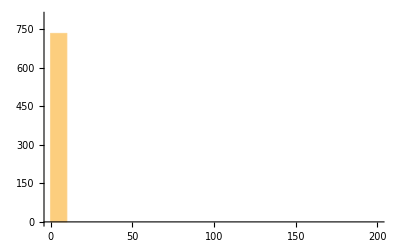
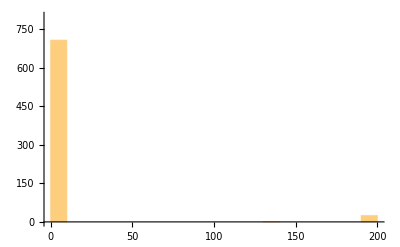
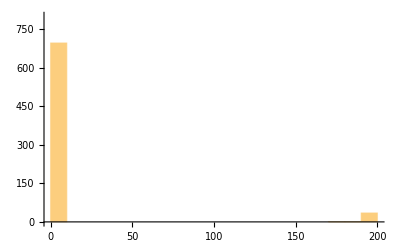
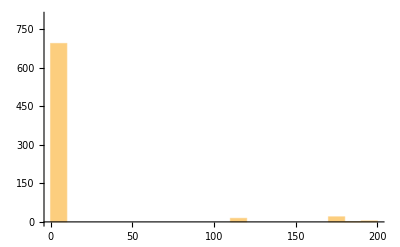
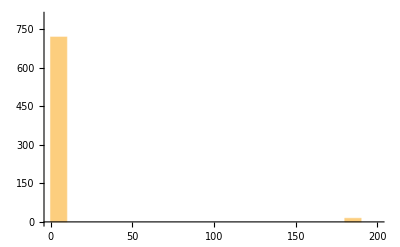
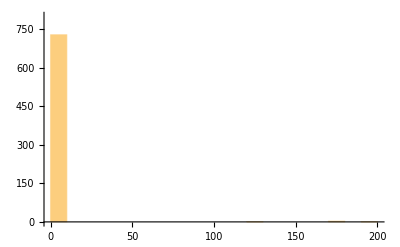
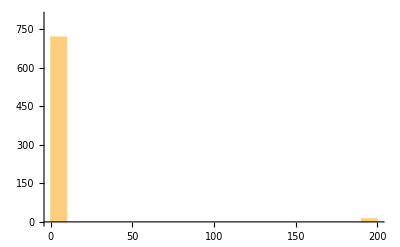
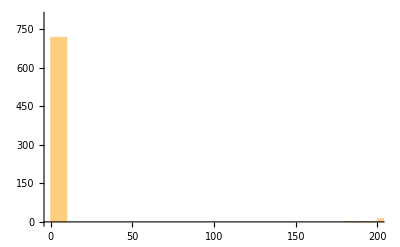
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[Histogram[(TestCALifeTime/@populationresponse[pcarus, RandomChoice[cancerperts]][[All, 1]])/.-Infinity->0,{10}, PlotRange->{{0, 200}, {0, 800}}], 20]
```

#### Examination of cancerous perturbation

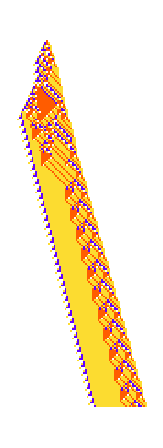

```mathematica
PlotCA[PerturbCA[{ca, ru}, 39->{{2},"Enumerate","AddValue"->1}]]
```

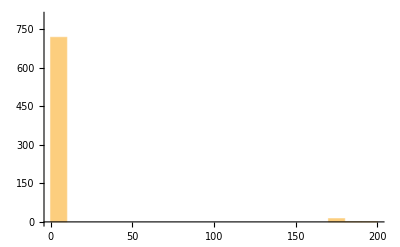

```mathematica
Histogram[(TestCALifeTime/@populationresponse[pcarus, rc][[All, 1]])/.-Infinity->0,{10}, PlotRange->{{0, 200}, {0, 800}}]
```

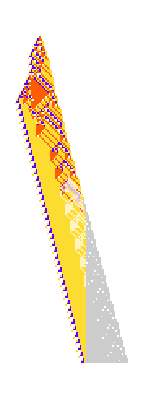
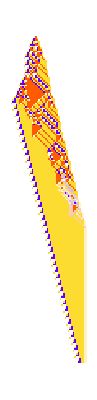
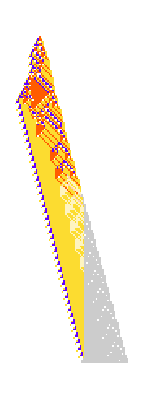
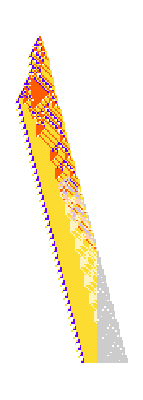
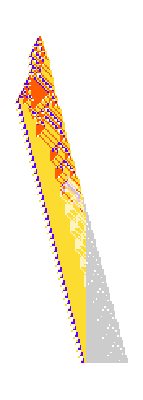
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{heal = RandomChoice[heals]},Table[With[{popru = RandomChoice[patients]}, With[{pca =  PerturbCA[{ca,popru}, rc]},
PlotDifferences[pca, PerturbCA[{pca, popru}, heal]]]], 50]]
```

### To therapies

54→{{11},Enumerate,AddValue→1}

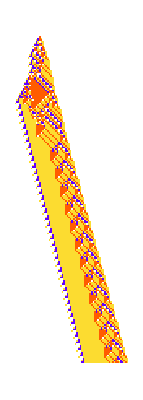

```mathematica
rc = RandomChoice[cancerperts]
sick = {PerturbCA[#, rc], #[[2]]}&/@ pcarus;
PlotCA[sick[[1, 1]]]
```

```mathematica
heals = Select[gethealers[{sick[[1, 1]], ru}], #[[1]]>rc[[1]]&];
```

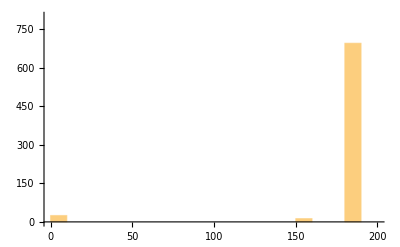
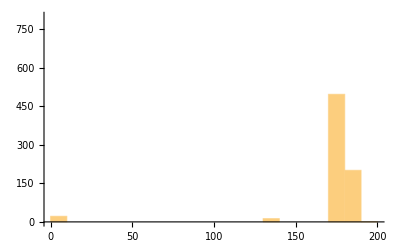
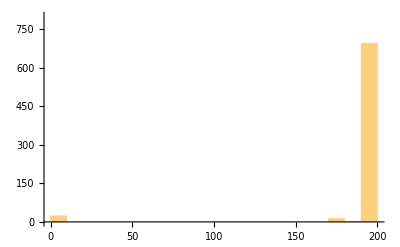
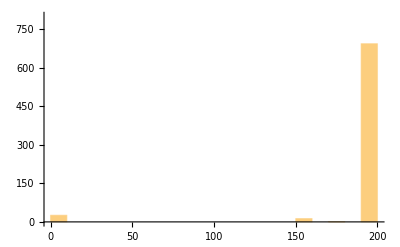
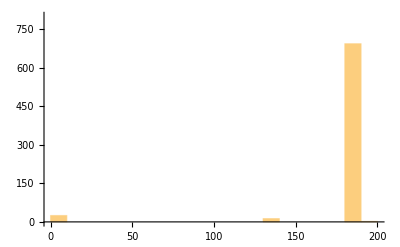
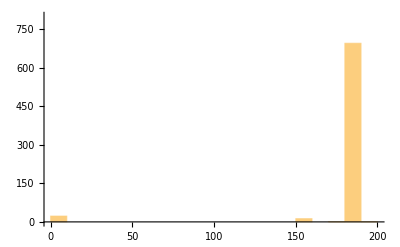
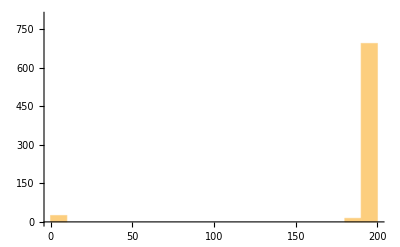
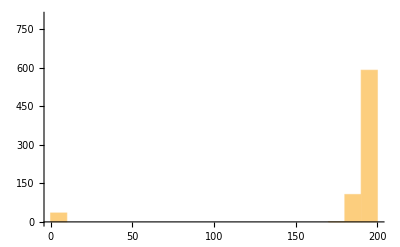

```mathematica
ParallelTable[Histogram[(TestCALifeTime/@populationresponse[sick, RandomChoice[heals]][[All, 1]])/.-Infinity->0,{10}, PlotRange->{{0, 200}, {0, 800}}], 20]
```

### Therapy Sensitivity for different diseases

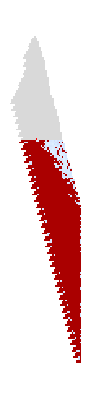
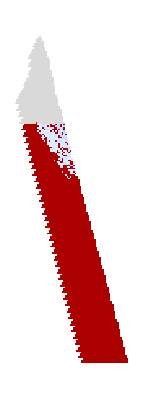
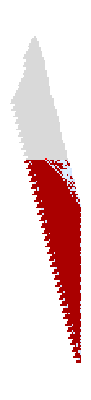
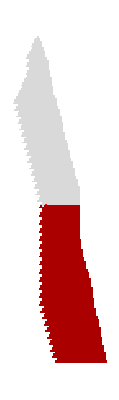
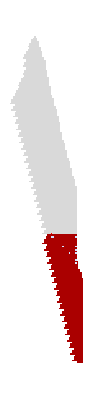
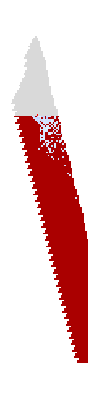
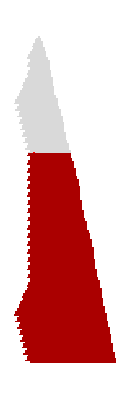
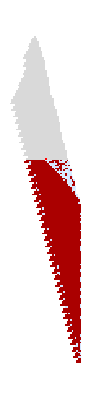

```mathematica
ParallelTable[TherapySensitivityPlot[ru,  RandomChoice[cancerperts]], 10]
```

## Population Responses For Other Rules

### Getting fitness-neutral group

```mathematica
ng2 = NestGraph[getallneutral, {k4rob[[sirob[[4]], 1]]}, 3];
```

```mathematica
patients = VertexList[ng2]
```

{{25188170208739390129512598335163286300,4,1},{25188170208739390129512615927349330716,4,1},{25188170208739390129512633519535375132,4,1},{25188170208739390129512651111721419548,4,1},{25188170208739390129521605534418027292,4,1},{25188170208739390129530612733672768284,4,1},{25188170208739390129548627132182250268,4,1},{25188170208739390129566641530691732252,4,1},{25208939396173529440026720320480166684,4,1},{25229708583607668750540842305797047068,4,1},{25250477771041808061054964291113927452,4,1},{25188170208739390129530630325858812700,4,1},{25188170208739390129548644724368294684,4,1},{25188170208739390129566659122877776668,4,1},{25208939396173529440026737912666211100,4,1},{25229708583607668750540859897983091484,4,1},{25250477771041808061054981883299971868,4,1},{25188170208739390129530647918044857116,4,1},{25188170208739390129548662316554339100,4,1},{25188170208739390129566676715063821084,4,1},{25208939396173529440026755504852255516,4,1},{25229708583607668750540877490169135900,4,1},{25250477771041808061054999475486016284,4,1},{25188170208739390129530665510230901532,4,1},{25188170208739390129548679908740383516,4,1},{25188170208739390129566694307249865500,4,1},{25208939396173529440026773097038299932,4,1},{25229708583607668750540895082355180316,4,1},{25250477771041808061055017067672060700,4,1},{25188170208739390129539619932927509276,4,1},{25188170208739390129557634331436991260,4,1},{25188170208739390129575648729946473244,4,1},{25208939396173529440035727519734907676,4,1},{25229708583607668750549849505051788060,4,1},{25250477771041808061063971490368668444,4,1},{25208939396173529440044734718989648668,4,1},{25229708583607668750558856704306529052,4,1},{25250477771041808061072978689623409436,4,1},{25208939396173529440062749117499130652,4,1},{25229708583607668750576871102816011036,4,1},{25250477771041808061090993088132891420,4,1},{25208939396173529440080763516008612636,4,1},{25229708583607668750594885501325493020,4,1},{25250477771041808061109007486642373404,4,1},{25208939396173529440044752311175693084,4,1},{25229708583607668750558874296492573468,4,1},{25250477771041808061072996281809453852,4,1},{25208939396173529440044769903361737500,4,1},{25229708583607668750558891888678617884,4,1},{25250477771041808061073013873995498268,4,1},{25208939396173529440044787495547781916,4,1},{25229708583607668750558909480864662300,4,1},{25250477771041808061073031466181542684,4,1},{25208939396173529440053741918244389660,4,1},{25229708583607668750567863903561270044,4,1},{25250477771041808061081985888878150428,4,1},{25208939396173529440062766709685175068,4,1},{25229708583607668750576888695002055452,4,1},{25250477771041808061091010680318935836,4,1},{25208939396173529440062784301871219484,4,1},{25229708583607668750576906287188099868,4,1},{25250477771041808061091028272504980252,4,1},{25208939396173529440062801894057263900,4,1},{25229708583607668750576923879374144284,4,1},{25250477771041808061091045864691024668,4,1},{25208939396173529440071756316753871644,4,1},{25229708583607668750585878302070752028,4,1},{25250477771041808061100000287387632412,4,1},{25208939396173529440080781108194657052,4,1},{25229708583607668750594903093511537436,4,1},{25250477771041808061109025078828417820,4,1},{25208939396173529440080798700380701468,4,1},{25229708583607668750594920685697581852,4,1},{25250477771041808061109042671014462236,4,1},{25208939396173529440080816292566745884,4,1},{25229708583607668750594938277883626268,4,1},{25250477771041808061109060263200506652,4,1},{25208939396173529440089770715263353628,4,1},{25229708583607668750603892700580234012,4,1},{25250477771041808061118014685897114396,4,1}}

```mathematica
pcarus = {getca[#], #}&/@ patients;
```

```mathematica
cancerperts = getcancerperts@pcarus[[1]];
```

Responses to disease

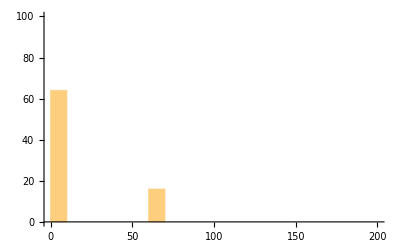
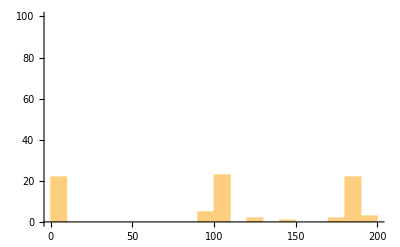
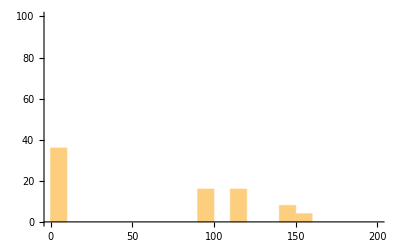
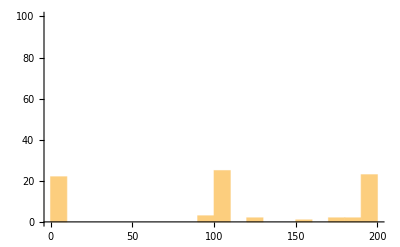
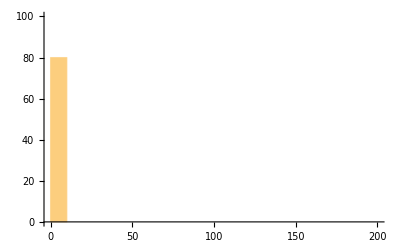
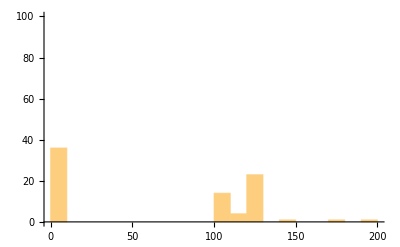
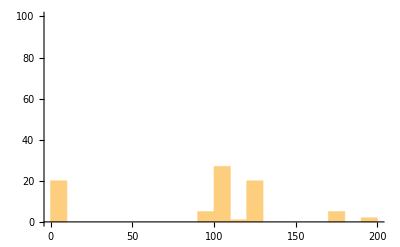
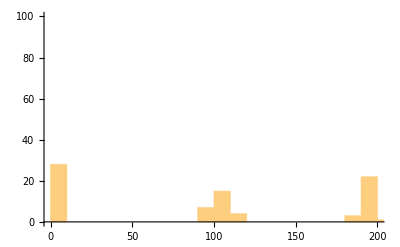
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[Histogram[(TestCALifeTime/@populationresponse[pcarus, #][[All, 1]])/.-Infinity->0,{10}, PlotRange->{{0, 200}, {0, 100}}]&, cancerperts]
```

#### Responses to therapy

```mathematica
rc = RandomChoice[cancerperts]
sick = {PerturbCA[#, rc], #[[2]]}&/@ pcarus;
PlotCA[sick[[1, 1]]]
```

```mathematica
heals = Select[gethealers[{sick[[1, 1]], ru}], #[[1]]>rc[[1]]&];
```

```mathematica
PlotCA/@sick[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Examination of cancerous perturbation

```mathematica
PlotCA[PerturbCA[{getca[k4rob[[sirob[[4]], 1]]], k4rob[[sirob[[4]], 1]]}, rc]]
```

-Graphics-

```mathematica
Histogram[(TestCALifeTime/@populationresponse[pcarus, rc][[All, 1]])/.-Infinity->0,{10}, PlotRange->{{0, 200}, {0, 100}}]
```

-Graphics-

```mathematica
Module[{heal = RandomChoice[heals]},Table[With[{popru = RandomChoice[patients]}, With[{pca =  PerturbCA[{getca[k4rob[[sirob[[4]], 1]]],popru}, rc]},
PlotDifferences[pca, PerturbCA[{pca, popru}, heal]]]], 50]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Population Response to different therapies

```mathematica
ParallelTable[Histogram[(TestCALifeTime/@populationresponse[sick, RandomChoice[heals]][[All, 1]])/.-Infinity->0,{10}, PlotRange->{{0, 200}, {0, 100}}], 20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Perturbation Sensitivity Across Population

```mathematica
GraphicsRow[ParallelMap[PerturbationSensitivityPlot[#, absdeltalt, ("AddValue"->1)]& , RandomSample[pcarus, 20]]]
```

-Graphics-

### Therapy Sensitivity to different diseases

```mathematica
PlotCA[sick[[1, 1]]]
```

-Graphics-

```mathematica
TherapySensitivityPlot[ru, rc]
```

-Graphics-

```mathematica
ParallelTable[TherapySensitivityPlot[k4rob[[sirob[[4]], 1]],  RandomChoice[cancerperts]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Updated Perturbation Sensitivity Plot

```mathematica
GraphicsRow@{PlotCA[getca[#[[1]], 200]], PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]}&@k4rob[[sirob[[15]]]]
```

-Graphics-

```mathematica
PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}, absdeltalt,"Random", "Trim"->{1,3}]&@k4rob[[sirob[[6]]]]
```

-Graphics-

```mathematica
PerturbationSensitivityPlot[{ getca[#[[1]], 400],#[[1]]}, absdeltalt,"Random", "Trim"->{1,3}]&@k4rob[[sirob[[6]]]]
```

-Graphics-

## Testing whether robustness is in the pattern or just the size

```mathematica
psprob = ParallelMap[PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]&,k4rob[[sirob]]];
```

```mathematica
Partition[psrob, 15] // GraphicsGrid
```

-Graphics-

And now regular (sorted) for comparison:

```mathematica
pspreg = ParallelMap[PerturbationSensitivityPlot[{ getca[#[[1]], 400],#[[1]]}]&,k4reg][[sireg]];
```

$Aborted

```mathematica
PerturbationSensitivityPlot[{getca[#[[1]], 400],#[[1]]}]&[k4reg[[sireg[[-3]]]]]
```

-Graphics-

```mathematica
Partition[pspreg, 15] // GraphicsGrid
```

-Graphics-

## Looking for Signs of Life in different rules

```mathematica
Transpose@{RandomInteger[{1, 201}, 100], RandomInteger[{1, 401}, 100]}
```

{{156,9},{137,220},{147,189},{27,164},{59,281},{149,153},{122,392},{62,161},{177,397},{83,253},{159,35},{66,43},{137,104},{183,83},{14,375},{125,304},{72,113},{96,189},{18,61},{169,239},{136,75},{39,364},{56,289},{186,231},{85,377},{19,23},{4,150},{36,197},{178,351},{83,394},{53,386},{105,88},{19,267},{23,340},{132,23},{168,169},{3,254},{157,358},{130,127},{191,379},{9,123},{33,75},{153,172},{189,322},{27,288},{25,141},{77,381},{120,397},{97,275},{177,81},{194,83},{12,396},{133,280},{95,307},{27,319},{15,370},{60,355},{33,78},{142,49},{130,382},{82,276},{40,217},{173,309},{175,135},{65,52},{174,106},{47,340},{127,350},{52,143},{198,109},{147,289},{85,259},{122,117},{10,334},{186,376},{122,248},{162,223},{180,222},{37,352},{196,78},{21,362},{22,228},{34,39},{181,93},{46,145},{192,208},{78,391},{119,172},{85,397},{195,273},{194,281},{71,265},{40,29},{87,398},{179,7},{18,39},{198,312},{179,222},{54,173},{173,40}}

```mathematica
4^3
```

64

```mathematica
3^3
```

27

```mathematica
randomrule[k_, r_]:= {FromDigits[Append[RandomInteger[{0, k - 1}, k^(2r+1) - 1], 0], k], k, r}
```

```mathematica
randomrule[2, 2]
```

{780665894,2,2}

```mathematica
SeedRandom[686450];
cr = randomrule[2, 2]
Table[
Echo[cr = randomrule[4, 1]];
(*cr = {110,2,1}*)
coords = Transpose@{RandomInteger[{1, 251}, 500], RandomInteger[{1, 500}, 500]};
reps = #->Red&/@ coords;
ArrayPlot@ReplacePart[PerturbCA[{getca[cr, 250], cr},coords, "BitFunc"->"SetValue"->1], reps], 10]
```

{1294788318,2,2}

{77116143920274950230764309057349533960,4,1}

{265494593332860780006927945372033590148,4,1}

{65707919867388656819660927666849528844,4,1}

{154706011244594209909460447807763658496,4,1}

{243732016263813908980219875516436299012,4,1}

{168952707506899978246064779276496573128,4,1}

{94780501382259224380069488096577398388,4,1}

{121623175765260044944944529210076858916,4,1}

{49848161434880693878236783558213271796,4,1}

{336866728296060711301899328642111028164,4,1}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA@getca[{3019941697641,3,1}]
```

-Graphics-

```mathematica
SeedRandom[686452];
Table[
cr = {{"[◼]", "RandomRuleMutation"}}[{3019941697641,3,1}];
coords = Transpose@{RandomInteger[{1, 1000}, 500], RandomInteger[{1, 200}, 500]};
reps = #->Red&/@ coords;
ArrayPlot@ReplacePart[PerturbCA[{getca[cr, 1000, 200], cr},coords, "BitFunc"->"SetValue"->2], reps], 50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cr = {3019941697641,3,1};
coords = Transpose@{RandomInteger[{1, 251}, 500], RandomInteger[{1, 500}, 500]};
reps = #->Red&/@ coords;
ArrayPlot@getca[cr, 250]
```

-Graphics-

## Michael Levin Connections

## Testing k = 5 perturbed evolution

## Responses to Different Diseases in Population

## Cancerous Rules for All Robust

Our goal here is to understand what’s

## Genetic Diseases